```mathematica
PinwheelArea[alpha_,beta_,a_]:= Module[{gamma,b,c,ap,bp,cp,alphap,betap,gammap,ra,rb,rc,tha,thb,thc,e,la,lb,lc,print},
print=False;
e = Sin[Pi/5];
gamma = Pi/5 - (alpha+beta);
alphap = 2Pi/5 - alpha;
betap = 2Pi/5-beta;
gammap = 2Pi/5 - gamma;
b = a * Sin[betap]/Sin[alphap];
c = a * Sin[gammap]/Sin[alphap];
ap = e - a;
bp = e - b;
cp = e - c;
tha = ArcTan[ap/rho];
thb = ArcTan[bp/rho];
thc = ArcTan[cp/rho];
ra = ap/Sin[tha];
rb = bp/Sin[thb];
rc = cp/Sin[thc];
la =Sqrt[1+rb^2 - 2 rb Cos[Pi/2-thb+alpha+3Pi/10]];
lb = Sqrt[1+rc^2 - 2rc Cos[Pi/2-thc + beta+3Pi/10]];
lc = Sqrt[1+ra^2 - 2 ra Cos[Pi/2-tha+gamma+3Pi/10]];
If[print,Print[{e,{a,b,c},{ap,bp,cp},{alpha,beta,gamma},{alphap,betap,gammap},{tha,thb,thc},{ra,rb,rc},{la,lb,lc}}//N]];
area[la,lb,lc]
];
```

```mathematica
arc[1.86,1.72,2.1]
```

1.25157

```mathematica
area[1.86,1.86,1.86]
```

1.49805

```mathematica
area[2rho,2rho,2.1]
```

1.29262

```mathematica
Clear[interp];
interp[p1_,p2_,x_]:= Module[{x1,y1,x2,y2},
{x1,y1}=p1;
{x2,y2}=p2;
(y2-y1)/(x2-x1) (x - x1) + y1];
```

```mathematica
interp[{1.878,1.237},{2.1,1.291},2]
```

1.26668

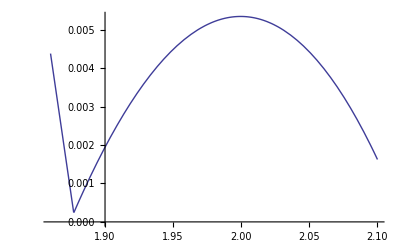

```mathematica
Plot[Max[1.237,area[2rho,2rho,x]]-interp[{1.878,1.237},{2.1,1.291},x],{x,1.86,2.1}]
```

```mathematica
0.
```

```mathematica
pinwheelarea[0.209439510239319421,0.209439510239319532,0.181048620887643535]
```

1.2848445560030345

```mathematica
D[area[u,u,x],{x,2}]//Simplify//Factor
```

-(u^2 √((x^2 (4 u^2-x^2))/u^4) (6 u^2-x^2))/(2 (2 u-x)^2 (2 u+x)^2)

```mathematica
area[u,u,x]//Factor
```

1/4 u^2 √((x^2 (4 u^2-x^2))/u^4)

```mathematica
Minimize[{1/s1 + 1.0/t1,ArcTan[s1]+ArcTan[t1]≤ 2.2,1≤ s1,1≤ t1},{s1,t1}]
```

{1.01794,{s1→1.96476,t1→1.96476}}

```mathematica
(* save: calculation of local twist-max on interval *)
Clear[t];
epsI=N[5/1000,50];
piN = N[Pi,50];
epsII = Interval[{0,epsI}];
epsI2 = Interval[{-epsI,epsI}];
alphat=piN/5 + epsII+ t;
betat = 2piN/5+epsI2; (* fix betat *)
gammat = piN - (alphat+betat); 
xgammat = ee+epsI2;
alphap = epsII; (* fix alphap *)
gammap = 2piN/5 - alphat; (* relate two sides *)
betap = (piN/5 - (alphap+gammap)); (* drag betap*)
xgammap = ee +epsI2;
D[(tjarea[alphat,betat,xgammat]+
pinwheelarea[alphap,betap,xgammap]),t]/.{t->0}
```

```mathematica
(* save: calculation of local twist-max on interval *)
Clear[t];
epsI=N[5/1000,50];
piN = N[Pi,50];
epsII = Interval[{0,epsI}];
epsI2 = Interval[{-epsI,epsI}];
alphat=piN/5 + epsII+ t;
gammat = 2piN/5+epsI2; (* fix gammat *)
betat = piN - (alphat+gammat); 
xgammat = ee+epsI2;
betap = epsII; (* fix betap *)
gammap = 2piN/5 - alphat; (* relate two sides *)
alphap = (piN/5 - (betap+gammap)); (* drag alphap*)
xgammap = ee +epsI2;
D[(tjarea[alphat,betat,xgammat]+
pinwheelarea[alphap,betap,xgammap]),t]/.{t->0}
```

```mathematica
(* calculation of slider double lattice second derivative.  By symmetry there is a unique zero at t=0, so this gives local optimality. *)
epsI=N[1/50,50];
epsI2 = Interval[{-epsI,epsI}];
D[pinwheelarea[0,0,ee+epsI2+t]+pinwheelarea[0,0,ee+epsI2-t],{t,2}]/.t->0
```

Interval[{0.2870748239214178815701788443868756481071914133972,2.0465952255300542245831681144974245340491118188607}]

```mathematica
thetax[0,0]//N
```

{0.628319,-0.628319}

```mathematica
ellx[0,0]//N
```

1.61803

```mathematica
thetax[0.001,0.001]
```

{0.628201,-0.627201}

```mathematica
2Pi/5//N
```

1.25664

```mathematica
seta[2rho,1.72,2]
```

3.03381

```mathematica
seta[2rho,2.0 rho,1.9]
```

2.92805

```mathematica
thetax[0.1,0.2]
```

{-0.586193,-0.470444}

```mathematica
thetax[0.2,0.19]
```

{0.606955,-0.416955}

```mathematica
pinwheelarea[Pi/10-0.1,Pi/10-0.1,0.18]
```

1.28482

```mathematica
pinwheeledge[0.2,0.2,0.18]
```

{1.7187,1.71869,1.73018}

```mathematica
2Pi/5 - 0.2
```

1.05664

```mathematica
Pi/10//N
```

0.314159

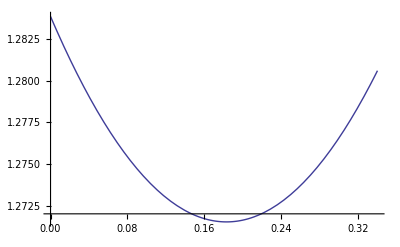

```mathematica
Plot[pinwheelarea[0.1,0.1,t],{t,0,0.34}]
```

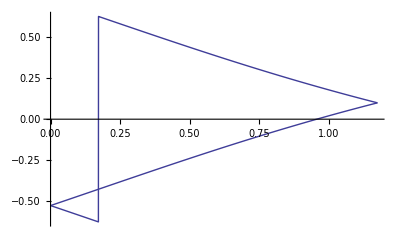

```mathematica
Plot[thetax[x,0.2],{x,0,2ee}]
```

```mathematica
4Sin[arc[2,2,2rho]//N]
```

2.95949

```mathematica
rho//N
```

0.809017

```mathematica
ArcSin[rho/2.0]
```

0.416441

```mathematica
areta[2rho,2rho,2]
```

0.968507301849241

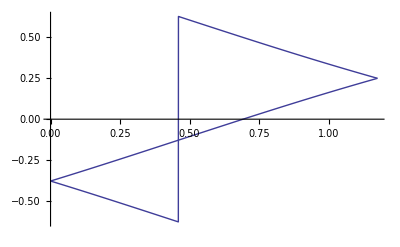

```mathematica
Plot[thetax[xalpha,0.5],{xalpha,0,2ee}]
```

```mathematica
?arc
```

arc[x,y,z] is the angle opposite z in a triangle with edges x y z.